```mathematica
ClearAll["Global`*"]

logSpace[start_,end_,num_]:=10^Range[start,end,(end-start)/(num-1)]

dir=NotebookDirectory[];
matrixFiles=FileNames["matrix_*.mx",dir];
matrices=Import/@matrixFiles;

wvals = SetPrecision[logSpace[-21,-17,Length[matrices]] ,150];
```

```mathematica
For[i = 1,i<Length[matrices]+1,i++,
Print[(matrices[[i,1,2]]^2 )/(matrices[[i,1,2]]^2 + matrices[[i,1,1]]^2)]
]
```

0.5006248051911620979

0.5006248051642011014

0.5006248048945911671

0.5006248021984949137

0.5006247752378413062

0.5006245056621976129

0.5006218129946880773

0.5005951949026545438

0.5003595733930725388

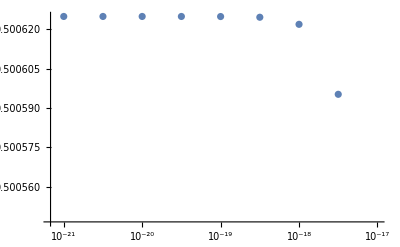

```mathematica
data = Table[
{wvals[[i]],(matrices[[i,1,2]]^2 )/(matrices[[i,1,2]]^2 + matrices[[i,1,1]]^2)},{i,1,Length[matrices]}
];
ListPlot[data,ScalingFunctions->{"Log",None},GridLinesStyle->Red]
```

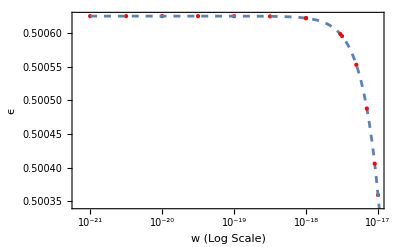

```mathematica
dataPlot=ListPlot[data,ScalingFunctions->{"Log",None},PlotStyle->{Red,PointSize[Medium]},FrameLabel->{"X (Log scale)","Y (Values)"},PlotRange->All];

D1 = Table[{x,interpFunc[x]},{x,10^-18,10^-17, 2 10^-18}];
dataPlot1=ListPlot[D1,ScalingFunctions->{"Log",None},PlotStyle->{Red,PointSize[Medium]},FrameLabel->{"X (Log scale)","Y (Values)"},PlotRange->All];


(*Create the interpolation function*)
interpFunc=Interpolation[data];

(*Create the Plot for the interpolation function with a dashed line*)
interpPlot=Plot[interpFunc[x],{x,10^-21,1.5 10^-17},PlotStyle->{Dashed},ScalingFunctions->{"Log",None},GridLines->Automatic,Frame->True,FrameLabel->{"X (Log scale)","Y (Values)"},PlotRange->All];

(*Combine the plots with a legend*)
ha = Show[dataPlot,interpPlot,dataPlot1,
Frame->{{True,False},{True,False}},
FrameLabel->{{"ϵ",None},{"w (Log Scale)",None}},
FontColor->Black,
FrameStyle->Directive[FontSize->14],
(*Adjust the font size as needed*)
BaseStyle->{FontSize->14}  (*Set the base font size for other text elements*)]
```

```mathematica
Export["plot.png",Show[dataPlot,interpPlot,dataPlot1,
Frame->{{True,False},{True,False}},
FrameLabel->{{"ϵ",None},{"w (Log Scale)",None}},
FontColor->Black,
FrameStyle->Directive[FontSize->21],
(*Adjust the font size as needed*)
BaseStyle->{FontSize->14}  (*Set the base font size for other text elements*)],ImageSize->800,ImageResolution->300]
```

plot.png